```mathematica
<<"/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
sysCI2EqNoise=DynamicalSystem[{
qa A(1-A-B)-qb A B+n(-A+((1-A-B))),
qb B(1-A-B)-qa B A+n(-B+((1-A-B)))},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{qa,0,10},{qb,0,10},{n,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{qa,qb,n}]

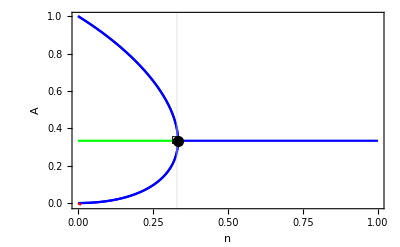

```mathematica
DisplayBifurcationDiagram[sysCI2EqNoise/.{qa->1,qb->1},n,StateVariables->{A},GridLines->{{0.33},{}}]
```

```mathematica
ER = EquilibriumBranches[sysCI2EqNoise/.{qa->1,qb->1},n];
ER[[1]][[4]][[4]]
```

{{0.333333333333349,0.333333333333318,0.333333333333333},{0.334529275588097,0.332138819649999,0.333331904761901},{0.33692542658911,0.329754097192863,0.333320476218026},{0.341734655867773,0.32500200983461,0.333263334297617},{0.351419709669436,0.315568364216871,0.333011926113693},{0.371047218995158,0.296991907689528,0.331960873315314},{0.392134540493583,0.277807823378783,0.330057636127634},{0.413558023779159,0.259099892753697,0.327342083467144},{0.435291436015209,0.240891023484422,0.323817540500368},{0.457308164860221,0.223203512145575,0.319488322994204},{0.479581251054383,0.206059016914305,0.314359732031312},{0.502083421430927,0.189478531050078,0.308438047518995},{0.524787122311842,0.173482357188648,0.301730520499511},{0.547664553247068,0.15809008248168,0.294245364271252},{0.57068770105587,0.14332055461249,0.28599174433164},{0.593828374128685,0.129191858717244,0.276979767154071},{0.617058236947465,0.115721295239895,0.26722046781264},{0.640348844782228,0.102925358747966,0.256725796469806},{0.663671678521339,0.0908197177351217,0.24550860374354},{0.686998179592872,0.0794191954352548,0.233582624971873},{0.710299784934292,0.0687377516715897,0.220962463394118},{0.733547961967629,0.0587884657630206,0.20766357226935},{0.756714243537333,0.0495835205086193,0.193702235954048},{0.779770262768011,0.0411341872699217,0.179095549962068},{0.802687787799381,0.033450812169261,0.163861400031358},{0.825438756355895,0.0265428034210461,0.148018440223059},{0.847995310108708,0.0204186198114993,0.131586070079793},{0.870329828787918,0.0150857603409589,0.114584410871123},{0.892414964003306,0.0105507550414296,0.0970342809552641},{0.91422367273216,0.00681915698062513,0.078957170287215},{0.935729250433178,0.00389553546229336,0.0603752141045284},{0.956905363745911,0.00178347043115065,0.0413111658229383},{0.97772608273569,0.000485548089275951,0.0217883691750344},{0.998165912644567,3.3577293327775×10^-6,0.00183072962609983},{1.,1.85719393260421×10^-29,0}}

```mathematica
combinedCIn = {}
For[i=1,i<=4,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

{}

```mathematica
theFile=File["/Volumes/My_Passport/argosim2/Runs/journal/data/bifqr1ds_basic/ci1_qa1.0_qb1_nvary.txt"]
Export[theFile,combinedCIn,"Table"];
```

File[/Volumes/My_Passport/argosim2/Runs/journal/data/bifqr1ds_basic/ci1_qa1.0_qb1_nvary.txt]

```mathematica
sysCI2EqNoisenoU=DynamicalSystem[{
qa A(1-A-B)-qb A B+n(-A+(B)),
qb B(1-A-B)-qa B A+n(-B+(A))
},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{qa,0,10},{qb,0,10},{n,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{qa,qb,n}]

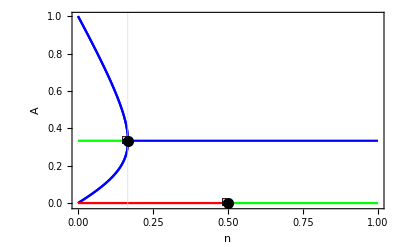

```mathematica
DisplayBifurcationDiagram[sysCI2EqNoisenoU/.{qa->1,qb->1},n,StateVariables->{A},GridLines->{{0.166},{}}]
```

```mathematica
ER = EquilibriumBranches[sysCI2EqNoisenoU/.{qa->1,qb->1},n];
ER[[1]][[7]][[4]]
```

{{0,0,0.5},{-0.00119665589099379,0.00119379876650376,0.500001428562245},{-0.00359849991744197,0.00357278722948363,0.500012856343979},{-0.00843602219613121,0.0082960701193795,0.500069976038376},{-0.01,0.0098039592470361,0.500098020376482}}

```mathematica
combinedCIn = {}
For[i=1,i<=7,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

{}

```mathematica
theFile=File["/Volumes/My_Passport/argosim2/Runs/journal/data/bifqr1ci2_basic/ci2_qa1.0_qb1_nvary.txt"]
Export[theFile,combinedCIn,"Table"];
```

File[/Volumes/My_Passport/argosim2/Runs/journal/data/bifqr1ci2_basic/ci2_qa1.0_qb1_nvary.txt]

```mathematica
sysDSEqNoise=DynamicalSystem[{
qa A (1-A)- qb A(1-A)+n((1-A)-A)
},
{{A,-0.01,1+0.01}},
{{qa,0,10},{qb,0,10},{n,0,1}}]
```

DynamicalSystem[«1 ODE»,{A},{qa,qb,n}]

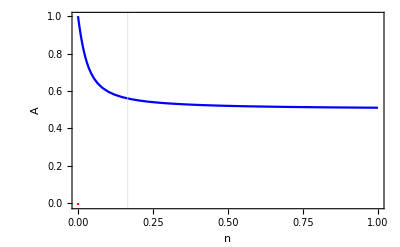

```mathematica
DisplayBifurcationDiagram[sysDSEqNoise/.{qa->1,qb->0.92},n,StateVariables->{A},GridLines->{{0.166},{}}]
```

```mathematica
ER = EquilibriumBranches[sysDSEqNoise/.{qa->1,qb->0.82},n];
ER[[1]][[3]][[4]]
```

Part::partw: Part 3 of {EquilibriumBranch[Stable,n,{{0.522454621099216,1},...,«40»}],EquilibriumBranch[Unstable,n,{\*RowBox[{"{", RowBox[{RowBox[{"-", "0.01`"}], ",", "0.0017823529411764709378410991435149923`15.9…1003"}], "}"}]\),...,{-5.9420741428941×10^-23,0}}]} does not exist.

Part::partw: Part 4 of {EquilibriumBranch[Stable,n,{{0.522454621099216,1},...,«40»}],EquilibriumBranch[Unstable,n,{\*RowBox[{"{", RowBox[{RowBox[{"-", "0.01`"}], ",", "0.0017823529411764709378410991435149923`15…003"}], "}"}]\),...,{-5.9420741428941×10^-23,0}}]}⟦3⟧ does not exist.

{EquilibriumBranch[Stable,n,{{0.522454621099216,1},...,{1.,0}}],EquilibriumBranch[Unstable,n,{{-0.01,0.00178235294117647},...,{-5.9420741428941×10^-23,0}}]}⟦3⟧⟦4⟧

```mathematica
combinedCIn = {}
For[i=1,i<=2,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

{}

```mathematica
theFile=File["/Volumes/My_Passport/argosim2/Runs/journal/data/bifqr0.82ds_basic/ds_qa1.0_qb0.82_nvary.txt"]
Export[theFile,combinedCIn,"Table"];
```

File[/Volumes/My_Passport/argosim2/Runs/journal/data/bifqr0.82ds_basic/ds_qa1.0_qb0.82_nvary.txt]